```mathematica
(*F = ma sprendinys*)
Clear[F,m,c]
(*Solve the differential equation*)
sol1=DSolve[{z''[t]==F/m*Sqrt[(1-(t*z''[t]/c)^2)],z[0]==0,z'[0]==0},z[t],t]
sol1a = DSolve[{z''[t]==F/m*Sqrt[(1-(z'[t]/c)^2)],z[0]==0,z'[0]==0},z[t],t]
D[D[sol1[[2]],t],t]
```

{{z[t]→-(c (√(c^2 m^2)-√(c^2 m^2+F^2 t^2)+F t ArcTanh[(F t)/(√(c^2 m^2+F^2 t^2))]))/F},{z[t]→(c (√(c^2 m^2)-√(c^2 m^2+F^2 t^2)+F t ArcTanh[(F t)/(√(c^2 m^2+F^2 t^2))]))/F}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z[t]→(-c^2 m+c^2 m Cos[(F t)/(c m)])/F},{z[t]→(c^2 m+c^2 m Cos[(-c m π+F t)/(c m)])/F}}

{z''[t]→1/F c ((F^4 t^2)/((c^2 m^2+F^2 t^2)^(3/2))-F^2/(√(c^2 m^2+F^2 t^2))+(F t ((3 F^5 t^3)/((c^2 m^2+F^2 t^2)^(5/2))-(3 F^3 t)/((c^2 m^2+F^2 t^2)^(3/2))))/(1-(F^2 t^2)/(c^2 m^2+F^2 t^2))-(F t ((2 F^4 t^3)/((c^2 m^2+F^2 t^2)^2)-(2 F^2 t)/(c^2 m^2+F^2 t^2)) (-(F^3 t^2)/((c^2 m^2+F^2 t^2)^(3/2))+F/(√(c^2 m^2+F^2 t^2))))/((1-(F^2 t^2)/(c^2 m^2+F^2 t^2))^2)+(2 F (-(F^3 t^2)/((c^2 m^2+F^2 t^2)^(3/2))+F/(√(c^2 m^2+F^2 t^2))))/(1-(F^2 t^2)/(c^2 m^2+F^2 t^2)))}

```mathematica
(*Define the parameters*)
(*F=10; (*Force*)*)
m=0.005; (*Mass*)
c=3*10^8; (*Speed of light*)
```

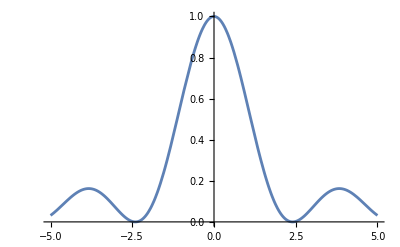

```mathematica
Plot[Abs[BesselJ[0,x]]^2,{x,-5,5}]
```

```mathematica
(*Duoda atstumą iki pirmo nulio*)
N[BesselJZero[0,1]]
```

2.40483

```mathematica
(* Burės paviršiaus plotas () *)
Sail=2*Pi*Integrate[x,{x,0,N[BesselJZero[0,1]]}]
```

18.1684

```mathematica
(*Intensyvumo funkcija paveikta x operatoriumi ir suintegruota.
Gaunasi vidutinė intensyvumo reikšmė per visą paviršių*)
Beselis=2*Pi*Integrate[x*Abs[BesselJ[0,x]]^2,{x,0,N[BesselJZero[0,1]]}]
```

4.89664

```mathematica
Clear[F]
P = 1000000; (*Beam overall power*)
(*Force acting on sail*)
F = 4*Pi*P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, N[BesselJZero[0,1]]}]
```

0.0326443

```mathematica
(*Extract the solution function*)
zSol[t_]=z[t]/. sol1[[2]];
(*Plot the solution*)
Manipulate[Plot[zSol[t],{t,0,tMax},PlotRange->{{0,tMax},Automatic},AxesLabel->{"t","z(t)"},PlotLabel->"Solution to the Differential Equation",GridLines->Automatic],
{{tMax,10,"Maximum Time"},1,1000,1}
]
```

```mathematica
(*Define the parameters*)
m= 0.01; (*mass*)
c=3*10^8; (*speed of light*)
w0=1; (*waist radius*)
n=1; (*refraction index*)
lam=600*10^-9; (*wavelength*)
P=100000000000; (*Bessel beam overall power*)
gRadius[z_]:=w0*Sqrt[1+(z^2)/Zr^2]; (*Gauss radius*)
Zr=N[Pi]*w0^2*n/lam; (*Rayleigh range*)
radius = 1;

(*Bessel part*)
I0 = 2*P/N[Pi]/w0^2; (*Beam overall power*)
(*Force acting on sail*)
F = P/c*Integrate[x*Abs[BesselJ[0,x]]^2, {x, 0, w0}]
500/3 (BesselJ[0,1]^2+BesselJ[1,1]^2)
(*Define the ODE with the new gIntensity[z[t]]*)
gIntensity[z_]:=I0/c*(w0/gRadius[z])^2*Exp[-2*r^2/gRadius[z]^2];
eqn=z''[t]*m/Sqrt[(1-(t*z''[t]/c)^2)]==Integrate[gIntensity[z[t]],{r,0,w0}];

(*Define the initial conditions*)
initialConditions={z'[0]==0,z[0]==0};
(*Solve the ODE numerically*)
Tmax=100; (*You can adjust this based on your problem*)
sol=NDSolve[{eqn,initialConditions},z,{t,0,Tmax}];
{z->InterpolatingFunction[…]}
```

500/3 (BesselJ[0,1]^2+BesselJ[1,1]^2)

500/3 (BesselJ[0,1]^2+BesselJ[1,1]^2)

{z→InterpolatingFunction[…]}

Part::partd: Part specification sol1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification sol1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 0.00204286 is not a valid variable.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 2.04286 is not a valid variable.

D::ivar: 4.08368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

Part::partd: Part specification sol1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 0.00204286 is not a valid variable.

D::dvar: Multiple derivative specifier {0.00204286,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 2.04286 is not a valid variable.

D::dvar: Multiple derivative specifier {2.04286,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::ivar: 4.08368 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {4.08368,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}] is not a valid replacement rule.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],{ImagePadding,ImageSize,AspectRatio}] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{System`Dump`opts}].

General::stop: Further output of Median::rectn will be suppressed during this calculation.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name]}}⟦All,All,2,1⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name]}}⟦All,All,2,1⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name]}}⟦All,All,2,2⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name]}}⟦All,All,2,2⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name]}}⟦All,All,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name]}}⟦All,All,2,1⟧ is not a valid Association or a list.

General::stop: Further output of DeleteMissing::invrp will be suppressed during this calculation.

-Graphics-

-Graphics-

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0,Tmax} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0,Tmax} is not a machine-sized real number.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0.0001,Tmax} is not a machine-sized real number.

Part::partd: Part specification sol1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0,Tmax} is not a machine-sized real number.

Part::partd: Part specification sol1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0,Tmax} is not a machine-sized real number.

Part::partd: Part specification sol1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {sol1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value Tmax in {t,0,Tmax} is not a machine-sized real number.

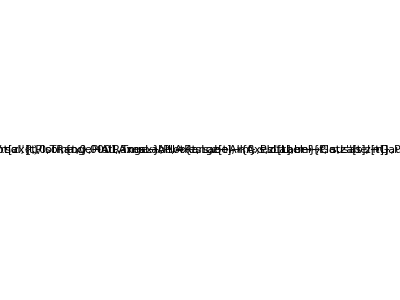

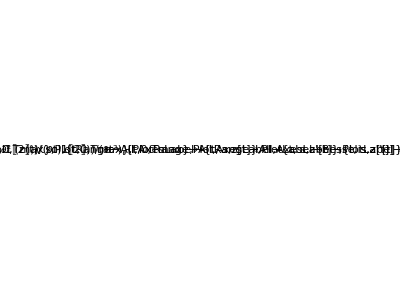

```mathematica
plot1=Plot[Evaluate[z[t]/. sol[[1]]],{t,0,Tmax},
PlotRange->All,AxesLabel->{"t, s","z[t], m"},PlotLabel->"Gausas z[t]"];

plot2=Plot[Evaluate[Derivative[1][z][t]/.sol[[1]]],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z'[t], m"},PlotLabel->"Gausas z'[t]"];

plot3=Plot[Evaluate[Derivative[2][z][t] /. sol[[1]]],{t,0.0001,Tmax},PlotRange->All,AxesLabel->{"t, s","z''[t], m"},PlotLabel->"Gausas z''[t]"]; 

plot4=Plot[Evaluate[z[t]/. sol1[[2]]],{t,0,Tmax},
PlotRange->All,AxesLabel->{"t, s","z[t]"},PlotLabel->"Besselis z[t]"];
plot5=Plot[Evaluate[D[z[t]/. sol1[[2]],t]],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z'[t]"},PlotLabel->"Besselis z'[t]"];
plot6=Plot[Evaluate[D[D[z[t]/.sol1[[2]],t],t]],{t,0,Tmax},PlotRange->All,AxesLabel->{"t, s","z''[t]"},PlotLabel->"Besselis z''[t]"];

GraphicsGrid[{{plot1,plot2,plot3}},Spacings->{0,0},ImageSize->Full]
GraphicsGrid[{{plot4,plot5,plot6}},Spacings->{0,0},ImageSize->Full]
plot1;
plot4;
```